```mathematica
(*Mathematica*)
```

```mathematica
(*Elliptic Curves McKean and Moll*)
```

```mathematica
(*Icosahedral group A_6*)
```

```mathematica
f[x_,y_]=x^6-y^6+5*x^2*y^2*(x^2-y^2)-4*x*y*(x^4*y^4-1)
```

x^6-y^6+5 x^2 y^2 (x^2-y^2)-4 x y (-1+x^4 y^4)

```mathematica
Reduce[f[x,y]==0,{x,y}]
```

y==Root[-x^6-4 x #1-5 x^4 #1^2+5 x^2 #1^4+4 x^5 #1^5+#1^6&,1]||y==Root[-x^6-4 x #1-5 x^4 #1^2+5 x^2 #1^4+4 x^5 #1^5+#1^6&,2]||y==Root[-x^6-4 x #1-5 x^4 #1^2+5 x^2 #1^4+4 x^5 #1^5+#1^6&,3]||y==Root[-x^6-4 x #1-5 x^4 #1^2+5 x^2 #1^4+4 x^5 #1^5+#1^6&,4]||y==Root[-x^6-4 x #1-5 x^4 #1^2+5 x^2 #1^4+4 x^5 #1^5+#1^6&,5]||y==Root[-x^6-4 x #1-5 x^4 #1^2+5 x^2 #1^4+4 x^5 #1^5+#1^6&,6]

```mathematica
w=Flatten[{x+I*y}/.NSolve[f[x,y],{x,y}]]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(121001 x)/175984-(92291 y)/87992 == 1.

{-3.27093-0.3228 ⅈ,-1.88293+1.79453 ⅈ,1.00109-1.60968 ⅈ,-0.822925-1.96352 ⅈ,0.598043+0.204104 ⅈ,-0.755134-1.65435 ⅈ,0.341567+0.0186212 ⅈ,-1.5307-0.730719 ⅈ,-0.814758+0.361426 ⅈ,-0.135323-0.864709 ⅈ}

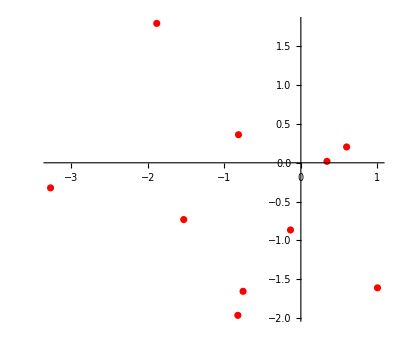

```mathematica
ComplexListPlot[w,PlotStyle->Red]
```

```mathematica
Length[w]
```

10

```mathematica
p[x_]=ExpandAll[Product[x-w[[i]],{i,10}]]
```

(14.0032-11.2247 ⅈ)-(43.3428-2.45784 ⅈ) x-(12.6709-99.0913 ⅈ) x^2+(106.758+48.881 ⅈ) x^3+(24.456-163.368 ⅈ) x^4-(206.104+111.442 ⅈ) x^5-(171.954-77.0076 ⅈ) x^6-(35.3384-92.1709 ⅈ) x^7+(12.0627+34.6663 ⅈ) x^8+(7.27201+4.7671 ⅈ) x^9+x^10

```mathematica
g[z_]=FullSimplify[f[Re[z],Im[z]]]
```

-Im[z]^6+4 Im[z] Re[z]-5 Im[z]^4 Re[z]^2+5 Im[z]^2 Re[z]^4-4 Im[z]^5 Re[z]^5+Re[z]^6

```mathematica
Reduce[-Im[z]^6+4 Im[z] Re[z]-5 Im[z]^4 Re[z]^2+5 Im[z]^2 Re[z]^4-4 Im[z]^5 Re[z]^5+Re[z]^6==0,z]
```

(Re[z]<-1&&(Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,1]||Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,2]))||z==-1-ⅈ||z==-1+ⅈ||(-1<Re[z]<0&&(Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,1]||Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,2]))||z==0||(0<Re[z]<1&&(Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,1]||Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,2]))||z==1-ⅈ||z==1+ⅈ||(Re[z]>1&&(Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,1]||Im[z]==Root[-Re[z]^6-4 Re[z] #1-5 Re[z]^4 #1^2+5 Re[z]^2 #1^4+4 Re[z]^5 #1^5+#1^6&,2]))

```mathematica
gout=ComplexPlot[-Im[z]^6+4 Im[z] Re[z]-5 Im[z]^4 Re[z]^2+5 Im[z]^2 Re[z]^4-4 Im[z]^5 Re[z]^5+Re[z]^6,{z,-3-3*I,3+3*I},ColorFunction->"CyclicReImLogAbs",ImageSize->2000];
```

```mathematica
(*Export["Galois_field_Polynomial_GF5_ComplexPlot.jpg",gout]*)
```

```mathematica
(*gout2=ComplexPlot[p[x],{x,-3-3*I,3+3*I},ColorFunction->"CyclicReImLogAbs",ImageSize->2000];*)
(*Export["Galois_field_Polynomial_GF5_ComplexPlot2.jpg",gout2]*)
```

```mathematica
(*g0=JuliaSetPlot[g[z],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All]*)
```

#### 3D Mandelbrot / Julia

```mathematica
(*Mandelbrot with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 25 Mov 2005 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 1024) && (Abs[nz-nzold]>10^(-3)),
		nzold=nz;
		nz=g[nz];
		++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3))||escapeCount>1000,escapeCount*Abs[Arg[nz]],escapeCount*Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]]]
]
```

```mathematica
FractalPure[m_][{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPure[m][{{-2.,2.,1000},{-2.,2.,1000}}];
```

```mathematica
g1=Rasterize[ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->2000],RasterSize->2000,ImageSize->2000];
```

```mathematica
g2=Rasterize[ListDensityPlot[Log[Abs[1/Max[arraym]+arraym-512/(arraym+Max[arraym])]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                 ColorFunction->(Hue[#^2+#]&),ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
colortab=Reverse[Union[{{0,0,0.1875},{0,0,0.20833333333333331},{0,0,0.22916666666666666},{0,0,0.25},{0,0,0.2708333333333333},{0,0,0.28125},{0,0,0.29166666666666663},{0,0,0.3125},{0,0,1/3},{0,0,0.34375},{0,0,0.375},{0,0,0.40625},{0,0,0.4375},{0,0,0.46875},{0,0,1/2},{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.020833333333333332,1/3},{0,0.03125,1/2},{0,0.041666666666666664,1/3},{0,0.0625,1/3},{0,0.0625,1/2},{0,0.0625,1},{0,0.08333333333333333,1/3},{0,0.09375,1/2},{0,0.10416666666666666,1/3},{0,0.125,1/3},{0,0.125,1/2},{0,0.125,1},{0,0.14583333333333331,1/3},{0,0.15625,1/2},{0,0.16666666666666666,1/3},{0,0.1875,1/3},{0,0.1875,1/2},{0,0.1875,1},{0,0.20833333333333331,1/3},{0,0.21875,1/2},{0,0.22916666666666666,1/3},{0,0.25,1/3},{0,0.25,1/2},{0,0.25,1},{0,0.2708333333333333,1/3},{0,0.28125,1/2},{0,0.29166666666666663,1/3},{0,0.3125,1/3},{0,0.3125,1/2},{0,0.3125,1},{0,1/3,1/3},{0,0.34375,1/2},{0,0.375,1/2},{0,0.375,1},{0,0.40625,1/2},{0,0.4375,1/2},{0,0.4375,1},{0,0.46875,1/2},{0,0.5,1},{0,1/2,1/2},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.,0.,0.375},{0.,0.,0.41666666666666663},{0.,0.,0.4583333333333333},{0.,0.,0.5},{0.,0.,0.5416666666666666},{0.,0.,0.5833333333333333},{0.,0.,0.625},{0.,0.,0.6666666666666666},{0.,0.041666666666666664,0.6666666666666666},{0.,0.08333333333333333,0.6666666666666666},{0.,0.125,0.6666666666666666},{0.,0.16666666666666666,0.6666666666666666},{0.,0.20833333333333331,0.6666666666666666},{0.,0.25,0.6666666666666666},{0.,0.29166666666666663,0.6666666666666666},{0.,0.3333333333333333,0.6666666666666666},{0.,0.375,0.6666666666666666},{0.,0.41666666666666663,0.6666666666666666},{0.,0.4583333333333333,0.6666666666666666},{0.,0.5,0.6666666666666666},{0.,0.5416666666666666,0.6666666666666666},{0.,0.5833333333333333,0.6666666666666666},{0.,0.625,0.6666666666666666},{0.,0.6666666666666666,0.6666666666666666},{0.020833333333333332,1/3,1/3},{0.03125,1/2,1/2},{0.041666666666666664,1/3,0.3125},{0.041666666666666664,0.6666666666666666,0.6666666666666666},{0.0625,1/3,0.29166666666666663},{0.0625,1/2,0.46875},{0.0625,1,1},{0.08333333333333333,1/3,0.2708333333333333},{0.08333333333333333,0.6666666666666666,0.625},{0.09375,1/2,0.4375},{0.10416666666666666,1/3,0.25},{0.125,1/3,0.22916666666666666},{0.125,1/2,0.40625},{0.125,0.6666666666666666,0.5833333333333333},{0.125,1,0.9375},{0.14583333333333331,1/3,0.20833333333333331},{0.15625,1/2,0.375},{0.16666666666666666,1/3,0.1875},{0.16666666666666666,0.6666666666666666,0.5416666666666666},{0.1875,0,0},{0.1875,1/3,0.16666666666666666},{0.1875,1/2,0.34375},{0.1875,1,0.875},{0.20833333333333331,0,0},{0.20833333333333331,1/3,0.14583333333333331},{0.20833333333333331,0.6666666666666666,0.5},{0.21875,1/2,0.3125},{0.22916666666666666,0,0},{0.22916666666666666,1/3,0.125},{0.25,0,0},{0.25,1/3,0.10416666666666666},{0.25,1/2,0.28125},{0.25,0.6666666666666666,0.4583333333333333},{0.25,1,0.8125},{0.2708333333333333,0,0},{0.2708333333333333,1/3,0.08333333333333333},{0.28125,0,0},{0.28125,1/2,0.25},{0.29166666666666663,0,0},{0.29166666666666663,1/3,0.0625},{0.29166666666666663,0.6666666666666666,0.41666666666666663},{0.3125,0,0},{0.3125,1/3,0.041666666666666664},{0.3125,1/2,0.21875},{0.3125,1,0.75},{0.3333333333333333,0.6666666666666666,0.375},{1/3,0,0},{1/3,0.020833333333333332,0},{1/3,0.041666666666666664,0},{1/3,0.0625,0},{1/3,0.08333333333333333,0},{1/3,0.10416666666666666,0},{1/3,0.125,0},{1/3,0.14583333333333331,0},{1/3,0.16666666666666666,0},{1/3,0.1875,0},{1/3,0.20833333333333331,0},{1/3,0.22916666666666666,0},{1/3,0.25,0},{1/3,0.2708333333333333,0},{1/3,0.29166666666666663,0},{1/3,0.3125,0},{1/3,1/3,0},{1/3,1/3,0.020833333333333332},{0.34375,0,0},{0.34375,1/2,0.1875},{0.375,0,0},{0.375,0.,0.},{0.375,1/2,0.15625},{0.375,0.6666666666666666,0.3333333333333333},{0.375,1,0.6875},{0.40625,0,0},{0.40625,1/2,0.125},{0.41666666666666663,0.,0.},{0.41666666666666663,0.6666666666666666,0.29166666666666663},{0.4375,0,0},{0.4375,1/2,0.09375},{0.4375,1,0.625},{0.4583333333333333,0.,0.},{0.4583333333333333,0.6666666666666666,0.25},{0.46875,0,0},{0.46875,1/2,0.0625},{0.5,0.,0.},{0.5,0.6666666666666666,0.20833333333333331},{0.5,1,0.5625},{1/2,0,0},{1/2,0.03125,0},{1/2,0.0625,0},{1/2,0.09375,0},{1/2,0.125,0},{1/2,0.15625,0},{1/2,0.1875,0},{1/2,0.21875,0},{1/2,0.25,0},{1/2,0.28125,0},{1/2,0.3125,0},{1/2,0.34375,0},{1/2,0.375,0},{1/2,0.40625,0},{1/2,0.4375,0},{1/2,0.46875,0},{1/2,1/2,0},{1/2,1/2,0.03125},{0.5416666666666666,0.,0.},{0.5416666666666666,0.6666666666666666,0.16666666666666666},{0.5625,0,0},{0.5625,1,0.5},{0.5833333333333333,0.,0.},{0.5833333333333333,0.6666666666666666,0.125},{0.625,0,0},{0.625,0.,0.},{0.625,0.6666666666666666,0.08333333333333333},{0.625,1,0.4375},{0.6666666666666666,0.,0.},{0.6666666666666666,0.041666666666666664,0.},{0.6666666666666666,0.08333333333333333,0.},{0.6666666666666666,0.125,0.},{0.6666666666666666,0.16666666666666666,0.},{0.6666666666666666,0.20833333333333331,0.},{0.6666666666666666,0.25,0.},{0.6666666666666666,0.29166666666666663,0.},{0.6666666666666666,0.3333333333333333,0.},{0.6666666666666666,0.375,0.},{0.6666666666666666,0.41666666666666663,0.},{0.6666666666666666,0.4583333333333333,0.},{0.6666666666666666,0.5,0.},{0.6666666666666666,0.5416666666666666,0.},{0.6666666666666666,0.5833333333333333,0.},{0.6666666666666666,0.625,0.},{0.6666666666666666,0.6666666666666666,0.},{0.6666666666666666,0.6666666666666666,0.041666666666666664},{0.6875,0,0},{0.6875,1,0.375},{0.75,0,0},{0.75,1,0.3125},{0.8125,0,0},{0.8125,1,0.25},{0.875,0,0},{0.875,1,0.1875},{0.9375,0,0},{0.9375,1,0.125},{1,0,0},{1,0,1},{1,1/100,81/100},{1,1/100,1},{1,1/25,16/25},{1,1/25,81/100},{1,1/25,1},{1,0.0625,0},{1,9/100,49/100},{1,9/100,16/25},{1,9/100,81/100},{1,9/100,1},{1,0.125,0},{1,4/25,9/25},{1,4/25,49/100},{1,4/25,16/25},{1,4/25,81/100},{1,4/25,1},{1,0.1875,0},{1,0.25,0},{1,1/4,1/4},{1,1/4,9/25},{1,1/4,49/100},{1,1/4,16/25},{1,1/4,81/100},{1,1/4,1},{1,0.3125,0},{1,9/25,4/25},{1,9/25,1/4},{1,9/25,9/25},{1,9/25,49/100},{1,9/25,16/25},{1,9/25,81/100},{1,9/25,1},{1,0.375,0},{1,0.4375,0},{1,49/100,9/100},{1,49/100,4/25},{1,49/100,1/4},{1,49/100,9/25},{1,49/100,49/100},{1,49/100,16/25},{1,49/100,81/100},{1,49/100,1},{1,0.5,0},{1,0.5625,0},{1,0.625,0},{1,16/25,1/25},{1,16/25,9/100},{1,16/25,4/25},{1,16/25,1/4},{1,16/25,9/25},{1,16/25,49/100},{1,16/25,16/25},{1,16/25,81/100},{1,16/25,1},{1,0.6875,0},{1,0.75,0},{1,81/100,1/100},{1,81/100,1/25},{1,81/100,9/100},{1,81/100,4/25},{1,81/100,1/4},{1,81/100,9/25},{1,81/100,49/100},{1,81/100,16/25},{1,81/100,81/100},{1,81/100,1},{1,0.8125,0},{1,0.875,0},{1,0.9375,0},{1,1,0},{1,1,1/100},{1,1,1/25},{1,1,0.0625},{1,1,9/100},{1,1,4/25},{1,1,1/4},{1,1,9/25},{1,1,49/100},{1,1,16/25},{1,1,81/100},{1,1,1}}]];
Length[%]


cf[l_]:=Block[{niv,rgb},niv=If[l<1/319,1,Ceiling[319*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

319

```mathematica
g3=Rasterize[ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Julia1000_Icosahedron_GF5_OutIn_Monitor_grid.jpg",GraphicsGrid[{{gout,g1},{g2,g3}},ImageSize->{4000,4000}]]
```

Julia1000_Icosahedron_GF5_OutIn_Monitor_grid.jpg

```mathematica
(*end*)
```